## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
```

```mathematica
(*Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]*)
```

```mathematica
<<"/home/strelda/Documents/programování/Mathematica/packages/GRQUICK/GRQUICKv4.m"
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-5/2-λ/4 | -χ/(2 √5) | -λ/(√10) | 0 | 0 | 0
-χ/(2 √5) | 1/20 (-30-13 λ-4 χ^2) | -(3 √2 χ)/5 | -(3 λ)/(5 √2) | 0 | 0
-λ/(√10) | -(3 √2 χ)/5 | 1/20 (-17 λ-2 (5+8 χ^2)) | -(3 χ)/2 | -(3 λ)/(5 √2) | 0
0 | -(3 λ)/(5 √2) | -(3 χ)/2 | 1/20 (10-17 λ-36 χ^2) | -(7 √2 χ)/5 | -λ/(√10)
0 | 0 | -(3 λ)/(5 √2) | -(7 √2 χ)/5 | 1/20 (30-13 λ-64 χ^2) | -(9 χ)/(2 √5)
0 | 0 | 0 | -λ/(√10) | -(9 χ)/(2 √5) | 5/2-λ/4-5 χ^2)

## Energies

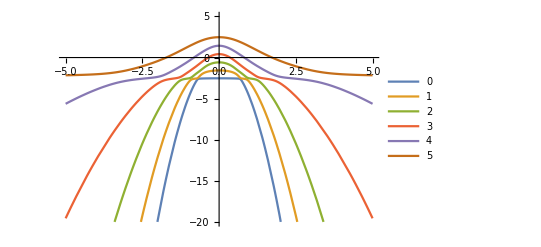

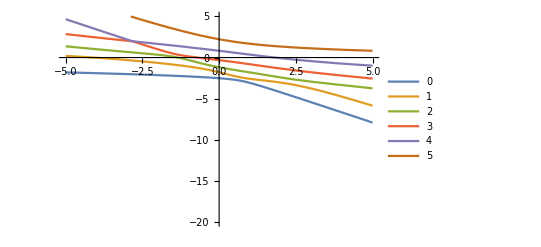

```mathematica
energies1=Eigenvalues[H[0.1,χ]];
energies2=Eigenvalues[H[λ,0.5]];
Plot[energies1,{χ,-5,5},PlotLegends->Range[0,10],PlotPoints->15,PlotRange->{Automatic,{-20,5}}]
Plot[energies2,{λ,-5,5},PlotLegends->Range[0,10],PlotPoints->5,PlotRange->{Automatic,{-20,5}}]
```

## Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{en,eigNon}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
eig=eigNon⟦#⟧/Norm[eigNon⟦#⟧]&/@Range[1,dim];
(*eig=Map[Normalize,eigNon];*)
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

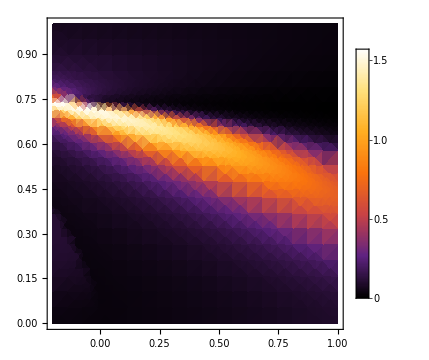
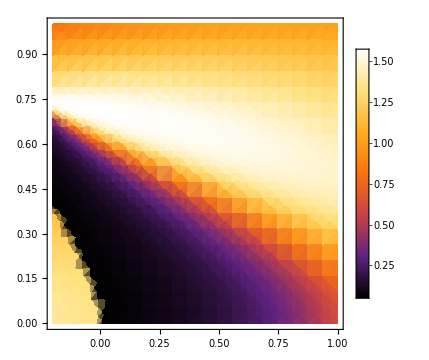
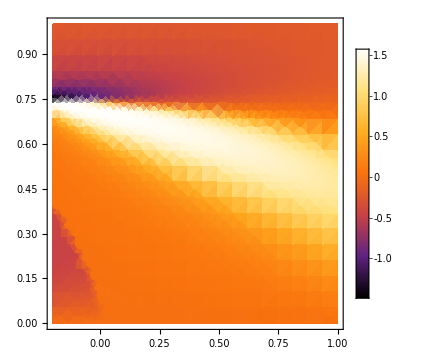

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
{DensityPlot[ArcTan[gC[y,x]⟦1,1⟧],{y,-0.2,1},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦2,2⟧],{y,-0.2,1},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦1,2⟧],{y,-0.2,1},{x,0,1},Evaluate@optDen]}
```

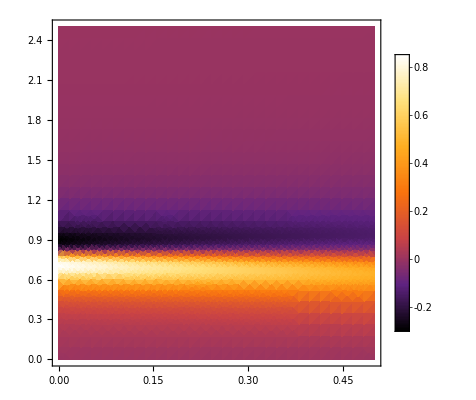

```mathematica
geodbg=DensityPlot[ArcTan@gC[λ,χ][[1]],{λ,0,0.5},{χ,0,2.5},Evaluate@densityPlotOptions,PlotPoints->30]
```

#### Metric tensor determinant

```mathematica
DensityPlot[Det[gC[x,l]],{x,0,2.5},{l,0,2},Evaluate@densityPlotOptions,PlotPoints->300,ScalingFunctions->"Log10",PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[Det[g[x,l]],{x,0,2.5},{l,0,2},Evaluate@font,PlotPoints->50,ScalingFunctions->"Log10",ColorFunction->"SunsetColors",AxesLabel->MaTeX/@{"\\lambda","\\chi","Det(g)"}]
```

-Graphics3D-

# Metric tensor using GRQUICK

## Interpolation of the metric tensor

Let' s interpolate them metric tensor components to get analytical prescription and save it to file for faster calculations.

```mathematica
gridStep=0.01;
λr={-1,1};
χr={0,1.5};
```

```mathematica
gTab=Flatten[Table[{λ,χ,gC[λ,χ]},{λ,λr[[1]],λr[[2]],gridStep},{χ,χr[[1]],χr[[2]],gridStep}],1];
```

```mathematica
Export[NotebookDirectory[]<>"gTab_n=2_gridStep=0,01.m",gTab];
```

```mathematica
gTab=Import[NotebookDirectory[]<>"gTab_n=2_gridStep=0,01.m"];
```

```mathematica
gTablen=Dimensions[gTab][[1]];
λS=gTab[[#]][[1]]&/@Range[1,gTablen];
χS=gTab[[#]][[2]]&/@Range[1,gTablen];
gS=gTab[[#]][[3]]&/@Range[1,gTablen];
gS11=gTab[[#]][[3]][[1,1]]&/@Range[1,gTablen];
gS12=gTab[[#]][[3]][[1,2]]&/@Range[1,gTablen];
gS22=gTab[[#]][[3]][[2,2]]&/@Range[1,gTablen];
```

-Graphics-

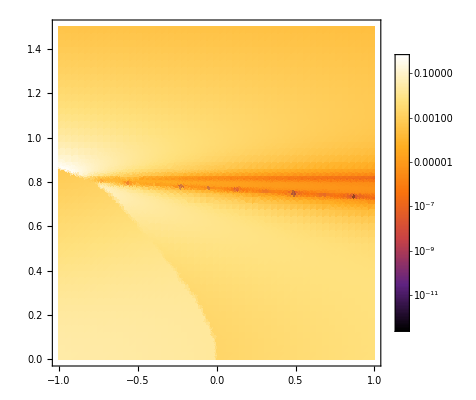

```mathematica
ListDensityPlot[Transpose@{λS,χS,Map[Det,gS]},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"]
DensityPlot[Det[gC[λ,χ]],Flatten@{λ,λr},Flatten@{χ,χr},Evaluate@densityPlotOptions,PlotPoints->50,ScalingFunctions->"Log10"]
```

```mathematica
interpolationMethod={InterpolationOrder->1,Method->"Spline"};
gI11=Interpolation[Transpose@{λS,χS,gS11},Evaluate@interpolationMethod];
gI12=Interpolation[Transpose@{λS,χS,gS12},Evaluate@interpolationMethod];
gI22=Interpolation[Transpose@{λS,χS,gS22},Evaluate@interpolationMethod];
gI[λ_,χ_]={{gI11[λ,χ],gI12[λ,χ]},{gI12[λ,χ],gI22[λ,χ]}};
```

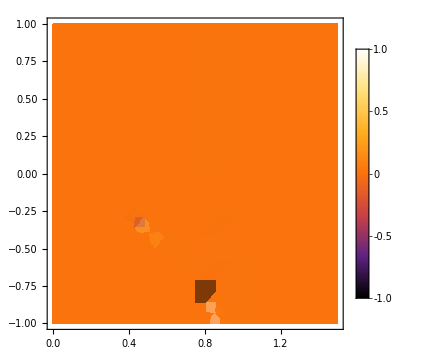
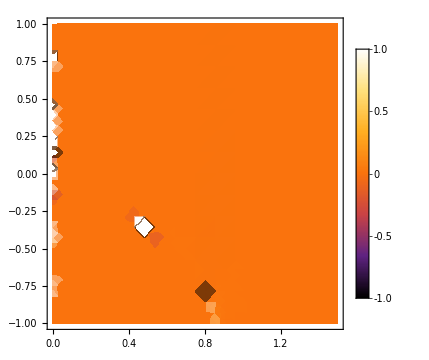
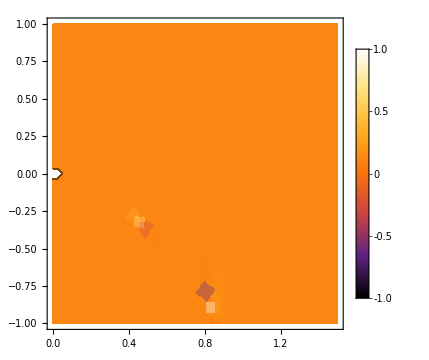

```mathematica
densitycheck={FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",ImageSize->Medium,PlotPoints->15,PlotRange->{Automatic,Automatic,{-1,1}},PlotLegends->BarLegend[{Automatic,{-1,1}}]};
Quiet@{DensityPlot[1-(gC[λ,χ][[1,1]])/gI11[λ,χ],Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck],
DensityPlot[1-(gC[λ,χ][[1,2]])/gI12[λ,χ],Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck],
DensityPlot[1-(gC[λ,χ][[2,2]])/gI22[λ,χ],Flatten@{χ,χr},Flatten@{λ,λr},Evaluate@densitycheck]}
```

## GRQUICK

```mathematica
Metin[gI[λ,χ],{λ,χ}]
```

Metric Success

```mathematica
Christoffel[{{0},{0,0}}]/.{λ->1,χ->1}
```

-0.508366

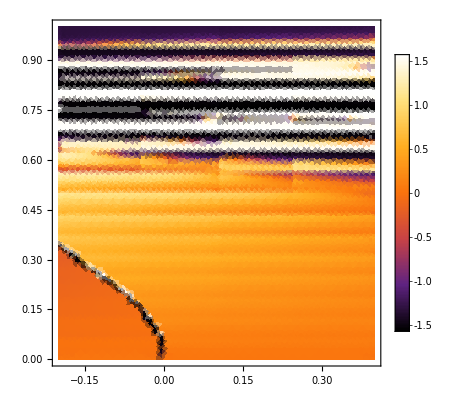

```mathematica
DensityPlot[ArcTan@Christoffel[{{0},{0,1}}],{λ,-0.2,0.4},{χ,0,1},Evaluate@densityPlotOptions,PlotPoints->30]
```

Geodesics finds the form for right side of the geodesic equation and geo[[1]], geo[[2]] as two interpolation type functions for λ[τ], χ[τ] and the boundary/initial value problem needs to be solved for geo[[1]] = 0, geo[[2]] = 0.

```mathematica
Einstein[0,0];
Setlight[1];
geo=Geodesics[τ];
eqn={geo[[1]]==0,geo[[2]]==0}/.{λ->λp,χ->χp};
```

```mathematica
τmax=100;
init={0,0};
```

```mathematica
denp=ListDensityPlot[Transpose@{λS,χS,Map[Det,gS]},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"];
(*denp=DensityPlot[Det[gI[λ,χ]],{λ,-0.5,1},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"];*)
```

### Initial value problem

```mathematica
cauchy[xi_,la_]:={χp[0]==init[[2]],χp'[0]==xi,λp[0]==init[[1]],λp'[0]==la,WhenEvent[χp[τ]<-0.1||χp[τ]>1||λp[τ]<-0.6||λp[τ]>300,"StopIntegration"]};
```

```mathematica
solMulti=Quiet@Table[NDSolve[Join[eqn,cauchy[Cos[θ],Sin[θ]]],{λp,χp},{τ,0,τmax}],{θ,0,π/2+π/10,π/10}];
```

```mathematica
parp=ParametricPlot[{λp[τ],χp[τ]}/.solMulti,{τ,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{denp,parp}]
```

-Graphics-

### Boundary value problem

```mathematica
final={0.7,0.2};
dirichlet={χp[0]==init[[2]],λp[0]==init[[1]],λp[τmax]==final[[1]],χp[τmax]==final[[2]],WhenEvent[χp[τ]<0||χp[τ]>1||λp[τ]<-0.6||λp[τ]>300,"StopIntegration"]};
dirichlet1={χp[0]==init[[2]],χp[τmax]==final[[2]],λp[0]==init[[1]],λp[τmax]==final[[1]]};
dirichletf[f_]:={λp[0]==init[[1]],χp[0]==init[[2]],λp[τmax]==final[[1]],χp[τmax]==f,WhenEvent[χp[τ]<0||χp[τ]>1||λp[τ]<-0.6||λp[τ]>300,"StopIntegration"]};
```

```mathematica
sol=Quiet@NDSolve[Join[eqn,dirichlet],{λp,χp},{τ,0,τmax},Method->"Shooting",AccuracyGoal->3,PrecisionGoal->3]
```

{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}}

```mathematica
solM=Quiet@NDSolve[Join[eqn,dirichletf[#]],{λp,χp},{τ,0,τmax},Method->"Shooting",AccuracyGoal->3,PrecisionGoal->3]&/@Range[0.1,0.5,0.4]
```

{{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}},{{λp→InterpolatingFunction[…],χp→InterpolatingFunction[…]}}}

```mathematica
(*sol=NDSolve[Join[eqn,dirichlet],{λp,χp},{τ,0,1},Method->{"Shooting","StartingInitialConditions"->{χp[0]==init[[1]],λp[0]==init[[2]],χp'[0]==1,λp'[0]==1}}]*)
```

```mathematica
parpB=ParametricPlot[{λp[τ],χp[τ]}/.solM,{τ,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{denp,parpB}]
```

-Graphics-

# Compiled geod function and Christoffel symbols

For huge matrices compute only first few energies and check for precission {vals,vecs}=Eigensystem[s,10]

Enable more functions to be compilable, for example Inverse

```mathematica
(*Internal`CompileValues[];(*to trigger auto-load*)ClearAttributes[Internal`CompileValues,ReadProtected];
syms=DownValues[Internal`CompileValues]/.HoldPattern[Verbatim[HoldPattern][Internal`CompileValues[sym_]]:>_]:>sym;
Complement[syms,Compile`CompilerFunctions[]]*)
```

## Defining compiled functions

```mathematica
derTerms=15;
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{c,l,dg,gInv},
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=Inverse[gC[λ,χ]];
{1/2 Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],1/2 Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],1/2 Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{c,l,dg,gInv},
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=Inverse[gC[λ,χ]];
{1/2 Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],1/2 Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],1/2 Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
(*G111[l_,x_]:=1/2 Inverse[gC[l,x]]⟦1,1⟧ND[gC[λ,x],λ,l,Terms->25]⟦1,1⟧+1/2 Inverse[gC[l,x]]⟦1,2⟧(2ND[gC[λ,x],λ,l,Terms->25]⟦2,1⟧-ND[gC[l,χ],χ,x,Terms->25]⟦1,1⟧)
G122[l_,x_]:=1/2 Inverse[gC[l,x]]⟦1,2⟧ND[gC[l,χ],χ,x,Terms->25]⟦2,2⟧+1/2 Inverse[gC[l,x]]⟦1,1⟧(2ND[gC[l,χ],χ,x,Terms->25]⟦1,2⟧-ND[gC[λ,x],λ,l,Terms->25]⟦2,2⟧)*)
```

Check Christoffel symbols. If wrong, increase derTerms.

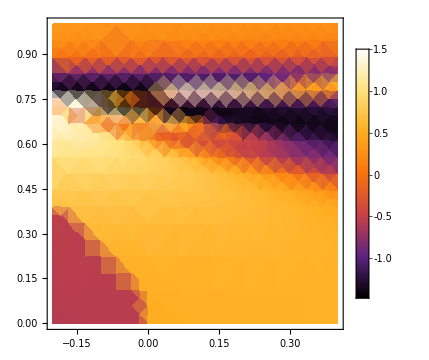
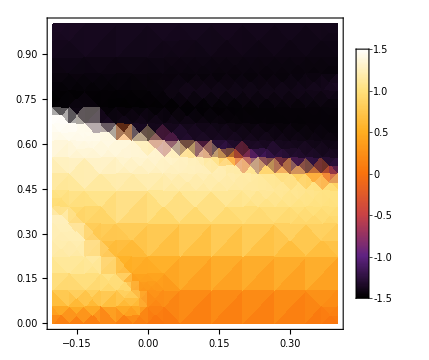
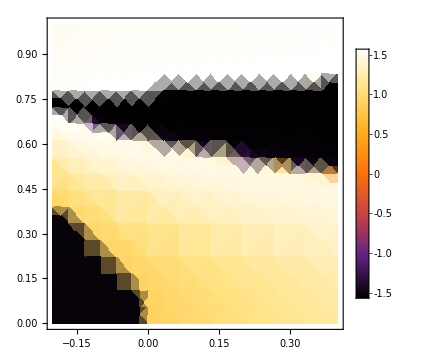

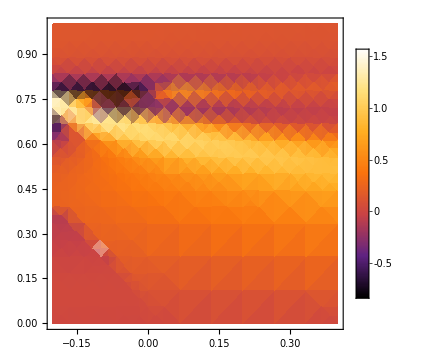
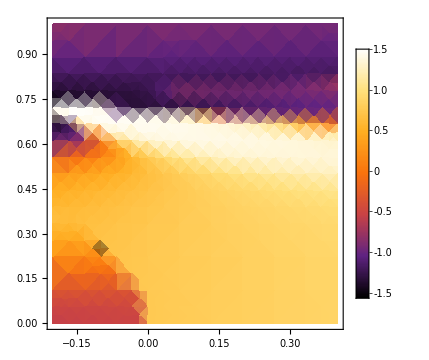
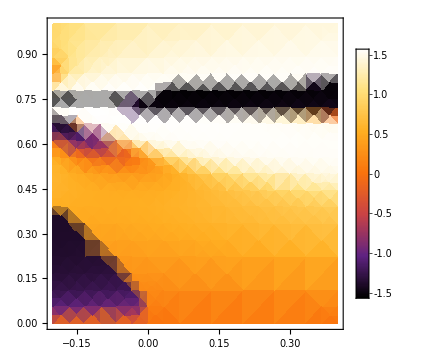

```mathematica
DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-0.2,0.4},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->10]&/@{1,2,3}
DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-0.2,0.4},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->10]&/@{1,2,3}
```

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-0.5,1},{χ,0,1.5},Evaluate@densityPlotOptions,ScalingFunctions->"Log10"];
```

```mathematica
τmax=10;
init={0.1,0.1};
eqn={χn''[τ]+G1[λn[τ],χn[τ]].{χn'[τ]^2,2 λn'[τ]χn'[τ],λn'[τ]^2}==0,
λn''[τ]+G2[λn[τ],χn[τ]].{ λn'[τ]^2,2 λn'[τ]χn'[τ], χn'[τ]^2}==0};
```

### Initial value problem

```mathematica
cauchy[la_,xi_]:={χn[0]==init[[1]],χn'[0]==xi,λn[0]==init[[2]],λn'[0]==la};
```

```mathematica
solMulti=Table[NDSolve[Join[eqn,cauchy[Cos[θ],Sin[θ]]],{λn,χn},{τ,0,τmax},Method->{"StiffnessSwitching","NonstiffTest"->False ,"DiscontinuityProcessing"->False}],{θ,0,π/2,π/20}];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 0.838779.

NDSolve::mxst: Maximum number of 10000 steps reached at the point τ == 0.970105.

$Aborted

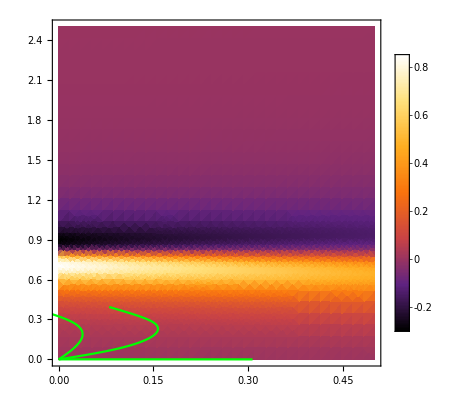

```mathematica
geodInitial=ParametricPlot[{λn[τ],χn[τ]}/.solMulti,{τ,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

### Boundary value problem

```mathematica
tmax=10;
eq={
χ''[t]+G1[λ[t],χ[t]].{χ'[t]^2,2 λ'[t]χ'[t],λ'[t]^2}==0,
λ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
sol=NDSolve[Join[eq,dirichlet[0,0,0.3,0.7]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2]
```

$Aborted

```mathematica
solM=NDSolve[Join[eq,dirichlet[0,0,0.3,#]],{λ,χ},{t,0,tmax}]&/@Range[0.1,1,0.2]
```

```mathematica
sol1=NDSolve[Join[eqn,dirichlet],{λn,χn},{τ,0,τmax},Method->{"StiffnessSwitching","NonstiffTest"->False ,"DiscontinuityProcessing"->False}]
```

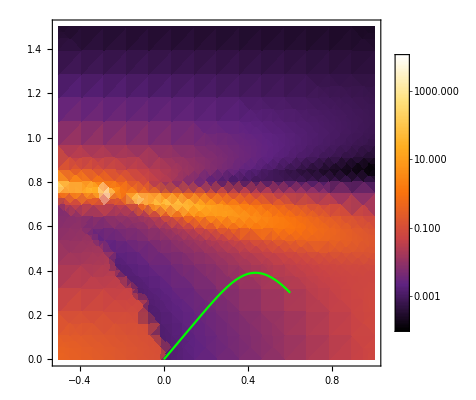

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM,{t,0,τmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```